# Range Expansion of Sea Otters along the California Coast Stochastic Process Final Project - Brooke Fitzgerald

## For my final project I wanted to look at stochastic models and how they are used to describe real world systems. In particular, I wanted to look at models of movement and how you can use randomness and stochasticity to describe the movement of organisms. When we’re talking about modeling organisms, it’s important to also talk about the scale at which you’re doing so. In general, there are three scales that you can use to describe ecological movement. The first scale is the microscopic. Modeling ecological systems at the microscopic scale consists of constructing individual trajectories from individual fluctuations. This type of modeling, while it maintains the most amount of detail about the system, it is the most mathematically intensive form of modeling and requires the most amount of input data. A mathematical description of microscopic modeling would be using stochastic differential equations describing the change of each particle and then using stochastic calculus to learn more about them. The second scale is the mesoscopic. Mesoscopic modeling simplifies microscopic models by representing individual fluctuations as probability density functions. Mesoscopic systems are only really suited for the description of a population of organisms because the probability density functions represent a statistical average of microscopic fluctuations and thus only hold at the population level. A mathematical description of mesoscopic models would be using integral equations to produce probability density functions from averaged fluction of individual trajectories. The final scale is the macroscopic. As the scales of microscopic and mesoscopic systems reaches an appropriate large limit, both systems converge to the corresponding macroscopic system. Macroscopic systems are the easiest to describe mathematically, as they are modeled with partial differential equations. Any of the information about individual motion is boiled down to the choice of parameters. For my project I decided to apply different models of ecological movement to the example of otter spread along the coast of California from 1914-1984. In the article “The Spread of a Reinvading Species: Range Expansion in the California Sea Otter,” authors Lubina and Levin analyzed published and unpublished data to analyze how the otters moved along the coast. In their article they used various statistical techniques to estimate rates of range expansion, and then used those rates as well as half the rate of change of the mean-squared deviation of individual positions to estimate the diffusion coefficient, which they calculated to be 104 km^2/yr for the entire range. However, they never actually used the diffusion equation beyond estimating the diffusion coefficient and discussing the implication for future modeling strategies. I decided to look at two different models and explore their various dynamics. Due to the lack of data on individual trajectories in the paper, I decided to use 2 different macroscopic models in order to explore different ecological scenarios.

```mathematica
data = List[{0,50},{24,310},{33,530},{36,660},{41,800},{43,880},{45,1050},{49,1190},{52,1260},{55,1390},{58,1530},{59,1720}];
```

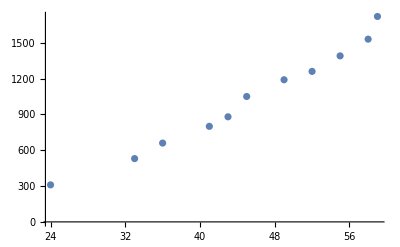

```mathematica
ListPlot[data,PlotRange->All]
```

## 1D General Diffusion Model with Advection Number density of otter population n(t,x) at time t: D = coefficient of diffusion, u = advective influence (drift) (∂n)/(∂t)=f(n,x,t)+D(∂^2 n)/(∂x^2)-u(∂n)/(∂x)

```mathematica
diff = 104;
rloc = .061;
u = 0.5;
```

```mathematica
eq= {D[n[x,t],t]==rloc*n[x,t]+diff*D[n[x,t],x,x]-u*D[n[x,t],x],n[0,t]==0, n[600,t] == 0, n[x,0]== Piecewise[{{5,295<x<305}},0]};
```

```mathematica
Off[NDSolve::mxsst]
sol=NDSolve[eq,n,{t,0,60},{x,0,600} ]; 
Plot3D[Evaluate[n[x,t]/.First[sol]],{t,0,60},{x,0,600},AxesLabel->{"t","x","n(t,x)"},PlotLabel->"Total Dispersion",PlotRange->All]
```

-Graphics3D-

```mathematica
a1 = NIntegrate[Evaluate[n[x,0]/.First[sol]],{x,0,600}];
a2 = NIntegrate[Evaluate[n[x,24]/.First[sol]],{x,0,600}];
a3 = NIntegrate[Evaluate[n[x,33]/.First[sol]],{x,0,600}];
a4 = NIntegrate[Evaluate[n[x,36]/.First[sol]],{x,0,600}];
a5 = NIntegrate[Evaluate[n[x,41]/.First[sol]],{x,0,600}];
a6 = NIntegrate[Evaluate[n[x,43]/.First[sol]],{x,0,600}];
a7 = NIntegrate[Evaluate[n[x,45]/.First[sol]],{x,0,600}];
a8 = NIntegrate[Evaluate[n[x,49]/.First[sol]],{x,0,600}];
a9 = NIntegrate[Evaluate[n[x,52]/.First[sol]],{x,0,600}];
a10 = NIntegrate[Evaluate[n[x,55]/.First[sol]],{x,0,600}];
a11 = NIntegrate[Evaluate[n[x,58]/.First[sol]],{x,0,600}];
a12 = NIntegrate[Evaluate[n[x,59]/.First[sol]],{x,0,600}];
```

```mathematica
diffData = Transpose[{{0,24,33,36,41,43,45,49,52,55,58,59},{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12}}];diffData//MatrixForm
```

(0 | 50.4405
24 | 216.627
33 | 375.211
36 | 450.568
41 | 611.255
43 | 690.581
45 | 780.198
49 | 995.872
52 | 1195.94
55 | 1436.23
58 | 1724.69
59 | 1833.19)

```mathematica
diffError = diffData[[All,2]]-data[[All,2]];
diffError = Function[x,x^2]/@diffError;
```

```mathematica
diffMSE = Mean[diffError]
```

26290.1

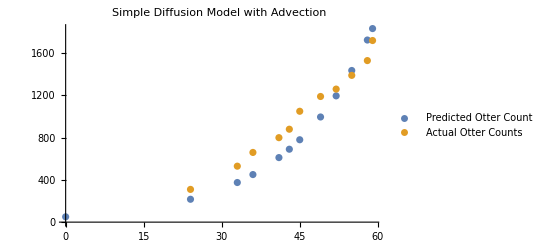

```mathematica
ListPlot[{diffData,data}, PlotLegends->{"Predicted Otter Count","Actual Otter Counts"},PlotLabel->"Simple Diffusion Model with Advection"]
```

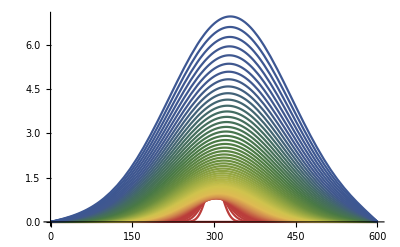

```mathematica
Show[Table[Plot[Evaluate[n[x,tt]/.First[sol]/.t->tt],{x,0,600},PlotRange->All,PlotStyle->ColorData["DarkRainbow",1-tt/60]],{tt,0,60}]]
```

```mathematica
FindRoot[Evaluate[n[x,59]/.First[sol]]==1,{x,100}]
FindRoot[Evaluate[n[x,59]/.First[sol]]==1,{x,500}]
```

{x→114.42}

{x→541.435}

```mathematica
diffRange = 541-114
diffRangeDiff = (541-300)-(300-114)
```

427

55

## 1D Chemotaxis Model with Local Growth Number density of otter population n(t,x) at time t: (∂n)/(∂t)=f(n,x,t)+D(∂^2 n)/(∂x^2)-χ(∂^2 c(x))/(∂x^2) , where χ represents the chemical coefficient.

```mathematica
chi = .022;
rloc = .061;
```

```mathematica
eq = {D[n[x,t],t]==rloc*n[x,t]+diff*D[n[x,t],x,x]+chi* D[(x-350)*n[x,t],x],n[0,t]==0, n[600,t] == 0, n[x,0]== Piecewise[{{5,295<x<305}},0]};
```

```mathematica
sol=NDSolve[eq,n,{t,0,60},{x,0,600}];
Plot3D[Evaluate[n[x,t]/.First[sol]],{t,0,60},{x,0,600},AxesLabel->{"t","x","n(x,t)"},PlotRange->All]
```

```mathematica
b1 = NIntegrate[Evaluate[n[x,0]/.First[sol]],{x,0,600}];
b2 = NIntegrate[Evaluate[n[x,24]/.First[sol]],{x,0,600}];
b3 = NIntegrate[Evaluate[n[x,33]/.First[sol]],{x,0,600}];
b4 = NIntegrate[Evaluate[n[x,36]/.First[sol]],{x,0,600}];
b5 = NIntegrate[Evaluate[n[x,41]/.First[sol]],{x,0,600}];
b6 = NIntegrate[Evaluate[n[x,43]/.First[sol]],{x,0,600}];
b7 = NIntegrate[Evaluate[n[x,45]/.First[sol]],{x,0,600}];
b8 = NIntegrate[Evaluate[n[x,49]/.First[sol]],{x,0,600}];
b9 = NIntegrate[Evaluate[n[x,52]/.First[sol]],{x,0,600}];
b10 = NIntegrate[Evaluate[n[x,55]/.First[sol]],{x,0,600}];
b11 = NIntegrate[Evaluate[n[x,58]/.First[sol]],{x,0,600}];
b12 = NIntegrate[Evaluate[n[x,59]/.First[sol]],{x,0,600}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {305.85}. NIntegrate obtained 50.4405 and 0.871638 for the integral and error estimates.

```mathematica
chemData = Transpose[{{0,24,33,36,41,43,45,49,52,55,58,59},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12}}];chemData//MatrixForm
```

(0 | 50.4405
24 | 216.642
33 | 375.242
36 | 450.596
41 | 611.283
43 | 690.602
45 | 780.222
49 | 995.874
52 | 1195.9
55 | 1436.08
58 | 1724.49
59 | 1832.98)

```mathematica
chemError = chemData[[All,2]]-data[[All,2]];
chemError = Function[x,x^2]/@chemError;
```

```mathematica
chemMSE = Mean[chemError]
```

26274.1

```mathematica
26274.07338945004`` 0.61
```

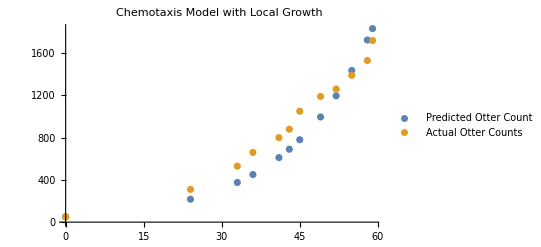

```mathematica
ListPlot[{chemData,data}, PlotLegends->{"Predicted Otter Count","Actual Otter Counts"},PlotLabel->"Chemotaxis Model with Local Growth"]
```

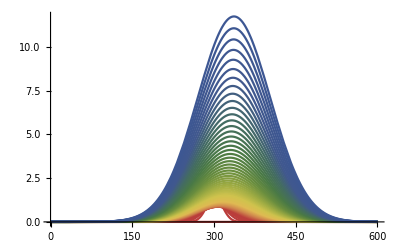

```mathematica
Show[Table[Plot[Evaluate[n[x,t]/.First[sol]/.t->tt],{x,0,600},PlotRange->All,PlotStyle->ColorData["DarkRainbow",1-tt/60]],{tt,0,60}]]
```

```mathematica
FindRoot[Evaluate[n[x,59]/.First[sol]]==1,{x,200}]
FindRoot[Evaluate[n[x,59]/.First[sol]]==1,{x,500}]
```

{x→191.338}

{x→481.345}

```mathematica
chemRange = (481-191)
chemRangeDiff = (481-300)-(300-191)
```

290

72

```mathematica
Conclusions:
As you can see from the graphs above, the diffusion model gives some probability of otters existing extremely far from Point Sur (where the otters were originally detected) while the chemotaxis model keeps the population more constrained geographically. Furthermore, the difference between the extent of the northern range and the southern range is 75 km in the paper, and thus the range of the chemotaxis model (72 km) more accurately reflects that range than the diffusion range (55 km). 

Thus, it is possible that chemotaxis might play an important role in otter spread.
```

```mathematica
Sources: 
Lubina, John A., and Simon A. Levin. "The spread of a reinvading species: range  expansion in the California sea otter." American Naturalist (1988): 526-543.

Méndez, Vicenç, Daniel Campos, and Frederic Bartumeus. Stochastic foundations in movement ecology: anomalous diffusion, front propagation and random searches. Springer Science & Business Media, 2013.
```